# Rovibrational Spectroscopy using Nikiforov-Uvarov Functional Analysis

## Raghav Sharma February–May 2024

```mathematica
(*Define subscripted symbols*)
Notation`AutoLoadNotationPalette=False;
<<Notation`;
ClearNotations[];
Symbolize/@{Subscript[E, 𝓃ℓ],Subscript[ψ, 𝓃ℓ],Subscript[D, e],Subscript[r, e],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3]};
```

## Part 2: NUFA Calculations

We use the parameters and energy equation found in Part-1: Algebra to solve for numerical values of energy eigenvalues and corresponding eigenfunctions.

#### Importing Data

```mathematica
(*Importing Dataset of Spectroscopic Constants*)
SetDirectory[NotebookDirectory[]];
molecularData=Import["molecular_data.csv", {"CSV","Dataset"},"HeaderLines"->{1,1}]
```

#### Molecular Parameters

```mathematica
molecule = "H2";
{Subscript[D, e],Subscript[r, e],μ,α}={"D_e","r_e","mu","alpha"}/.Normal[molecularData[molecule]];
μ=μ*9.3149410372*10^8; (*amu to eV/c^2*)
ℏ=1973.269804; (*eV A/c*)
```

#### NUFA Parameters

All assignments below are delayed. They are evaluated afresh each time they are called, so that we get correct values if we change the molecular parameters and quantum numbers.

```mathematica
β:=(2μ Subscript[r, e]^2)/(α^2 ℏ^2);
Subscript[X, 1]:=Subscript[D, e]+(ℓ(ℓ+1))/(α^2 β)(3/α^2-1/α);
Subscript[X, 2]:=-2 Subscript[D, e]+(ℓ(ℓ+1))/(α^2 β)(-6/α^2+4/α);
Subscript[X, 3]:=(ℓ(ℓ+1))/(α^2 β)(1+3/α^2-3/α);
λ:=√(β Subscript[X, 1]);
ν:=√(β (-Subscript[E, 𝓃ℓ]+Subscript[X, 3]));
```

```mathematica
(*Potential Function with Centrifugal Term (for plotting)*)
ModifiedMorse[r_]:=Subscript[D, e] ⅇ^(-2α(r-Subscript[r, e])/Subscript[r, e])-2 Subscript[D, e] ⅇ^(-α(r-Subscript[r, e])/Subscript[r, e])+ℏ^2/(2μ)(ℓ(ℓ+1))/r^2;
pekerisApproximated[r_]:=(Subscript[X, 1] z^2+Subscript[X, 2] z+Subscript[X, 3])/.{z->ⅇ^(-α(r-Subscript[r, e])/Subscript[r, e])};
```

#### Energy Eigenvalues

Define the quantum numbers 𝓃 and ℓ and call the expression below to get the eigenvalue.

```mathematica
Subscript[E, 𝓃ℓ]:=Subscript[X, 3]-1/β(1/2+𝓃+Subscript[X, 2]/2 √(β/Subscript[X, 1]))^2;
```

```mathematica
(*Example*)
𝓃=7;
ℓ=20;
StringForm["Energy Eigenvalue for `` under the Modified-Morse Potential; 𝓃 = ``, ℓ = ``: `` eV",molecule,𝓃,ℓ, NumberForm[Subscript[E, 𝓃ℓ],{20,8}]]
```

Energy Eigenvalue for H2 under the Modified-Morse Potential; 𝓃 = 3, ℓ = 25: 0.10775659 eV

#### Eigenfunctions

We use the expression for eigenfunctions given in Udoh et al. Their numerical values are too small to be plotted accurately, so we numerically integrate and normalize them. We also need to reverse the change of variables made in Part-1, i.e., z=ⅇ^((-α(r-r_e))/r_e) because we will be plotting the eigenfunctions along the r-axis.

```mathematica
(*Non-Normalized Eigenfunction*)
nonNormalizedEigenfunction[r_]:=FullSimplify[(ⅇ^(-λ z)z^ν Hypergeometric1F1[-𝓃,(1+2ν),2λ z])/.{z->ⅇ^(-α(r-Subscript[r, e])/Subscript[r, e])}];
(*Normalization Constant*)
𝒩:=NIntegrate[(nonNormalizedEigenfunction[r])^2,{r,0,∞}];
(*Normalized Eigenfunction*)
Subscript[ψ, 𝓃ℓ][r_]:=FullSimplify[1/(√𝒩)nonNormalizedEigenfunction[r]];
```

#### Tabulating and Plotting

```mathematica
(*Eigenvalues*)
𝓃Min=0;
𝓃Max=2;
ℓMin=0;
ℓMax=2;
Labeled[Grid[Table[NumberForm[Subscript[E, 𝓃ℓ],{20,7}],{𝓃,𝓃Min,𝓃Max},{ℓ,ℓMin,ℓMax}],Frame->All],StringForm["Energy Eigenvalues (eV) for `` under the Modified-Morse Potential", molecule],Top]
(*𝓃 on rows, ℓ on columns*)
```

-4.4760131 | -4.4612281 | -4.4317922
-3.9623153 | -3.9480810 | -3.9197402
-3.4799188 | -3.4662351 | -3.4389895Energy Eigenvalues (eV) for H2 under the Modified-Morse Potential

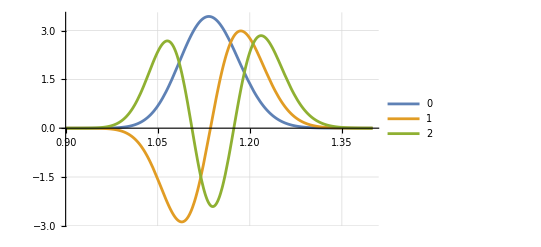

```mathematica
(*Eigenfunctions*)
ℓ=25;
Plot[Evaluate[Table[(Subscript[ψ, 𝓃ℓ][r]),{𝓃,0,2}]],{r,0.9,1.4},PlotRange->Full,PlotLegends->Range[0,2],GridLines->Automatic]
```

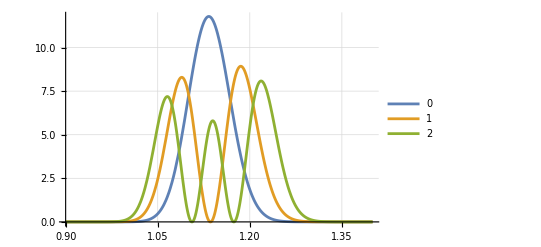

```mathematica
(*Probability Densities*)
Plot[Evaluate[Table[(Subscript[ψ, 𝓃ℓ][r])^2,{𝓃,0,2}]],{r,0.9,1.4},PlotRange->Automatic,PlotLegends->Range[0,2],GridLines->Automatic]
```

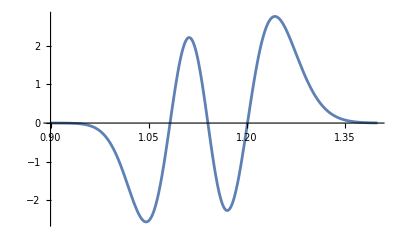

```mathematica
𝓃=3;
ℓ=2;

Plot[Evaluate[Subscript[ψ, 𝓃ℓ][r]],{r,0.9,1.4},PlotRange->Full]
```

```mathematica
nufaPlot:=Plot[Evaluate[Subscript[ψ, 𝓃ℓ][r]],{r,0.9,1.4},PlotRange->Full,PlotStyle->{Red,Thickness[0.001],Dashed}]
fdmPlot:=ListLinePlot[Thread[{rVals,1/(√step)eigenFunctions[[𝓃+1]]}], PlotRange->{{0.9,1.4},Full},PlotStyle->{Blue,Thickness[0.001],Dashed}]
```

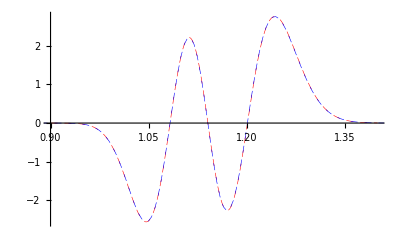

```mathematica
Show[Evaluate@{nufaPlot,fdmPlot}]
```